```mathematica
λ=10(10^-6); (* Plots behavior not affected by choice of wavelength since we are averaging over [a,a+λ] *)
q=(2Pi)/λ;
Vd=0.1;
δVg=0.1;
vg2=0.7;
vs=3800;
c=(3.4(8.85)(10^-12))/(25(10^-9));
e=1.602(10^-19);

dN[a_,b_,T_]:=(b-a)/(T-1);

Vg[v_,δ_,x_]:=v-δ Sin[q x];
n[v_,d_]:=c/e(v/2(1+Erf[v/(d √2)])+d/(√(2Pi))Exp[-v^2/(2 d^2)]);
p[v_,d_]:=-c/e(v/2(1-Erf[v/(d √2)])-d/(√(2Pi))Exp[-v^2/(2 d^2)]);
np[v_,d_]:=n[v,d]+p[v,d];
nm[v_,d_]:=n[v,d]-p[v,d];

A[v_,δ_,d_]:=1/λ NIntegrate[nm[Vg[v,δ,t],d]/np[Vg[v,δ,t],d],{t,0,λ}];
B[v_,δ_,d_]:=e/c 1/λ NIntegrate[1/(e/c np[Vg[v,δ,t],d]),{t,0,λ}];
F[v_,δ_,d_]:=c/e 1/λ NIntegrate[e/c nm[Vg[v,δ,t],d],{t,0,λ}];
G[v_,δ_,d_]:=c/e 1/λ NIntegrate[e/c np[Vg[v,δ,t],d],{t,0,λ}];
H[v_,δ_,d_]:=1/λ NIntegrate[D[nm[Vg[v,i,t],d]/np[Vg[v,i,t],d],i]/.i->δ,{t,0,λ}]; (* DA *)
J[v_,δ_,d_]:=e/c 1/λ NIntegrate[D[1/(e/c np[Vg[v,i,t],d]),i]/.i->δ,{t,0,λ}]; (* DB *)
```

```mathematica
j[v_,δ_,d_,x_]:=e vs(nm[Vg[v,δ,x],d]-A[v,δ,d]/B[v,δ,d]);
Subscript[j, aec][v_,δ_,d_]:=e vs c/e 1/λ NIntegrate[(c/e)^-1 nm[Vg[v,δ,t],d],{t,0,λ}]-e vs A[v,δ,d]/B[v,δ,d];
L[v_,δ_,d_]:=-(e vs)/(2δ) (B[v,δ,d]H[v,δ,d]-A[v,δ,d]J[v,δ,d])/(B[v,δ,d])^2;
```

```mathematica
(* Plot[{(c/e)^-1 nm[Vg[0.5,1.5,x],0.1],(c/e)^-1 np[Vg[0.5,1.5,x],0.1]},{x,-λ/4,3λ/4}]
Plot[{((c/e)^-1 nm[Vg[0.5,1.5,x],0.1])/((c/e)^-1 np[Vg[0.5,1.5,x],0.1]),1/((c/e)^-1 np[Vg[0.5,1.5,x],0.1])},{x,-λ/4,3λ/4},PlotRange->{-2,15}]
f[v_,δ_,d_]:=vs A[v,δ,d]/(F[v,δ,d]B[v,δ,d]);
Plot[1/vs f[0.1,2.0,d],{d,0,0.05},PlotRange->{0,0.23}] *)
```

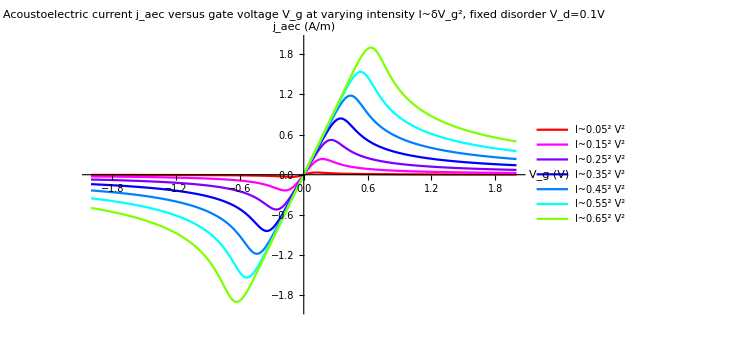

-Graphics-

```mathematica
Plot[{Subscript[j, aec][v,0.05,Vd],Subscript[j, aec][v,0.15,Vd],Subscript[j, aec][v,0.25,Vd],Subscript[j, aec][v,0.35,Vd],Subscript[j, aec][v,0.45,Vd],Subscript[j, aec][v,0.55,Vd],Subscript[j, aec][v,0.65,Vd]},{v,-2,2},PlotLegends->{"I~0.05^2 V^2","I~0.15^2 V^2","I~0.25^2 V^2","I~0.35^2 V^2","I~0.45^2 V^2","I~0.55^2 V^2","I~0.65^2 V^2"},PlotRange->{-2.0,2.0},PlotLabel->"Acoustoelectric current j_aec versus gate voltage V_g at varying intensity I~δV_g^2, fixed disorder V_d=0.1V",AxesLabel->{"V_g (V)","j_aec (A/m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
Plot[{Subscript[j, aec][e/c σ,0.05,Vd],Subscript[j, aec][e/c σ,0.15,Vd],Subscript[j, aec][e/c σ,0.25,Vd],Subscript[j, aec][e/c σ,0.35,Vd],Subscript[j, aec][e/c σ,0.45,Vd],Subscript[j, aec][e/c σ,0.55,Vd],Subscript[j, aec][e/c σ,0.65,Vd]},{σ,-(2c)/e,(2c)/e},PlotLegends->{"I~0.05^2 V^2","I~0.15^2 V^2","I~0.25^2 V^2","I~0.35^2 V^2","I~0.45^2 V^2","I~0.55^2 V^2","I~0.65^2 V^2"},PlotRange->{-2.0,2.0},PlotLabel->"Acoustoelectric current j_aec versus carrier number density difference n at varying intensity I~δV_g^2, fixed disorder V_d=0.1V",AxesLabel->{"n (m^-2)","j_aec (A/m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
(*Plot[{(e vs c/e)^-1 Subscript[j, aec][v,0.2,Vd],(e vs c/e)^-1 Subscript[j, aec][v,0.4,Vd],(e vs c/e)^-1 Subscript[j, aec][v,0.6,Vd],(e vs c/e)^-1 Subscript[j, aec][v,0.8,Vd],(e vs c/e)^-1 Subscript[j, aec][v,1.0,Vd],(e vs c/e)^-1 Subscript[j, aec][v,1.2,Vd]},{v,0,2},PlotLegends->{"I~0.2^2","I~0.4^2","I~0.6^2","I~0.8^2","I~1.0^2","I~1.2^2"},PlotRange->{0,0.6},PlotLabel->"Acoustoelectric current j_aec versus gate voltage V_g (V) at varying intensity I~δV_g^2, fixed disorder V_d=0.5 (V)",AxesLabel->{"V_g","j_aec"}]*)
```

```mathematica
datSlide3=Transpose[Prepend[Table[{σ,Subscript[j, aec][e/c σ,0.05,Vd],Subscript[j, aec][e/c σ,0.15,Vd],Subscript[j, aec][e/c σ,0.25,Vd],Subscript[j, aec][e/c σ,0.35,Vd],Subscript[j, aec][e/c σ,0.45,Vd],Subscript[j, aec][e/c σ,0.55,Vd],Subscript[j, aec][e/c σ,0.65,Vd]},{σ,-(2c)/e,(2c)/e,dN[-(2c)/e,(2c)/e,500]}]//N,{"n","I~0.05^2","I~0.15^2","I~0.25^2","I~0.35^2","I~0.45^2","I~0.55^2","I~0.65^2"}]];
Export["Desktop/Mathematica/Graphene Integrals/(Slide 3) Acoustoelectric current j_aec (A m^-1) versus carrier number density difference n (m^-2) at varying intensity I~δVg^2 (V^2), fixed disorder Vd=0.1V.txt",datSlide3]
```

Desktop/Mathematica/Graphene Integrals/(Slide 3) Acoustoelectric current j_aec (A m^-1) versus carrier number density difference n (m^-2) at varying intensity I~δVg^2 (V^2), fixed disorder Vd=0.1V.txt

```mathematica
nGaAs[n0_,δ_,x_]:=Max[0,n0-δ Sin[q x]];
(*jGaAs[n0_,δ_,x_]:=vs e(nGaAs[n0,δ,x]-1/NIntegrate[1/nGaAs[n0,δ,t],t,0,λ]);*)
j0GaAs2[n0_,δ_]:=vs e(1/λ NIntegrate[nGaAs[n0,δ,t],{t,0,λ}]-1/(1/λ NIntegrate[1/nGaAs[n0,δ,t],{t,0,λ}]));
j0GaAs1[n0_,δ_]:=vs e 1/λ(Integrate[n0-δ Sin[q t],{t,0,ArcSin[n0/δ]/q}]+Integrate[n0-δ Sin[q t],{t,(Pi-ArcSin[n0/δ])/q,λ}]); 
j0GaAs3[n0_,δ_]:=vs e δ^2/(2n0);
J0GaAs[n0_,δ_]:=Piecewise[{{j0GaAs1[n0,δ],0<=n0<=δ},{j0GaAs2[n0,δ],n0>δ}}];
Plot[{J0GaAs[σ,c/e 0.05],J0GaAs[σ,c/e 0.15],J0GaAs[σ,c/e 0.25],J0GaAs[σ,c/e 0.35],J0GaAs[σ,c/e 0.45],J0GaAs[σ,c/e 0.55],J0GaAs[σ,c/e 0.65]},{σ,0,(2c)/e},PlotLegends->{"I~0.05^2 V^2","I~0.15^2 V^2","I~0.25^2 V^2","I~0.35^2 V^2","I~0.45^2 V^2","I~0.55^2 V^2","I~0.65^2 V^2"},PlotRange->{0,3.0},PlotLabel->"(GaAs) Acoustoelectric current j_aec versus number density n_0 at varying intensity I~δV_g^2~δn^2",AxesLabel->{"n_0 (m^-2)","j_aec (A/m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
```

-Graphics-

```mathematica
datSlide2=Transpose[Prepend[Table[{σ,J0GaAs[σ,c/e 0.05],J0GaAs[σ,c/e 0.15],J0GaAs[σ,c/e 0.25],J0GaAs[σ,c/e 0.35],J0GaAs[σ,c/e 0.45],J0GaAs[σ,c/e 0.55],J0GaAs[σ,c/e 0.65]},{σ,0,(2c)/e,dN[0,(2c)/e,500]}]//N,{"n","I~0.05^2","I~0.15^2","I~0.25^2","I~0.35^2","I~0.45^2","I~0.55^2","I~0.65^2"}]];
Export["Desktop/Mathematica/Graphene Integrals/(Slide 2) (GaAs) Acoustoelectric current j_aec (A m^-1) versus carrier number density n_0 (m^-2) at varying intensity I~δVg^2~δn^2 (V^2).txt",datSlide2]
```

Desktop/Mathematica/Graphene Integrals/(Slide 2) (GaAs) Acoustoelectric current j_aec (A m^-1) versus carrier number density n_0 (m^-2) at varying intensity I~δVg^2~δn^2 (V^2).txt

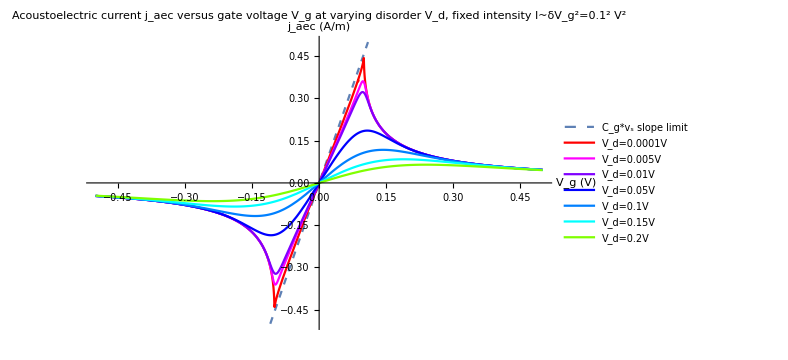

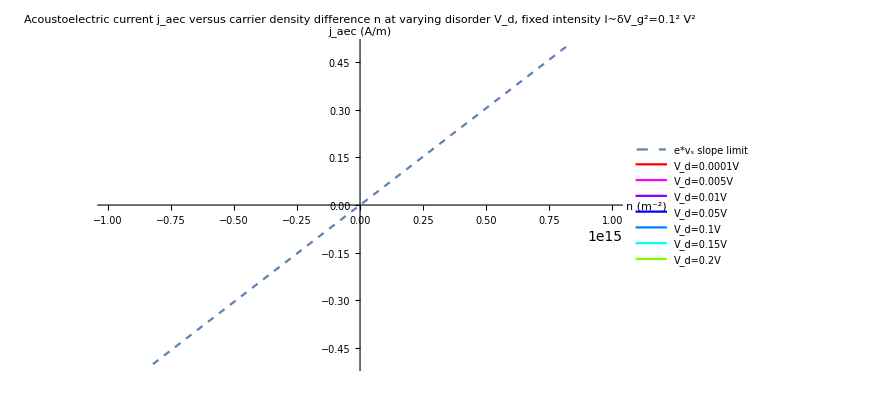

```mathematica
Plot[{c vs v,Subscript[j, aec][v,δVg,0.0001],Subscript[j, aec][v,δVg,0.005],Subscript[j, aec][v,δVg,0.01],Subscript[j, aec][v,δVg,0.05],Subscript[j, aec][v,δVg,0.1],Subscript[j, aec][v,δVg,0.15],Subscript[j, aec][v,δVg,0.2]},{v,-0.5,0.5},PlotRange->{-0.5,0.5},PlotLegends->{"C_g*v_s slope limit","V_d=0.0001V","V_d=0.005V","V_d=0.01V","V_d=0.05V","V_d=0.1V","V_d=0.15V","V_d=0.2V"},PlotLabel->"Acoustoelectric current j_aec versus gate voltage V_g at varying disorder V_d, fixed intensity I~δV_g^2=0.1^2 V^2",AxesLabel->{"V_g (V)","j_aec (A/m)"},PlotStyle->{Dashed,RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
Plot[{c vs e/c σ,Subscript[j, aec][e/c σ,δVg,0.0001],Subscript[j, aec][e/c σ,δVg,0.005],Subscript[j, aec][e/c σ,δVg,0.01],Subscript[j, aec][e/c σ,δVg,0.05],Subscript[j, aec][e/c σ,δVg,0.1],Subscript[j, aec][e/c σ,δVg,0.15],Subscript[j, aec][e/c σ,δVg,0.2]},{σ,-(0.5c)/e,(0.5c)/e},PlotRange->{-0.5,0.5},PlotLegends->{"e*v_s slope limit","V_d=0.0001V","V_d=0.005V","V_d=0.01V","V_d=0.05V","V_d=0.1V","V_d=0.15V","V_d=0.2V"},PlotLabel->"Acoustoelectric current j_aec versus carrier density difference n at varying disorder V_d, fixed intensity I~δV_g^2=0.1^2 V^2",AxesLabel->{"n (m^-2)","j_aec (A/m)"},PlotStyle->{Dashed,RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}] (* Join[{Dashed},Table[RGBColor[0,i,1],{i,0,1,1/2}],Table[RGBColor[0,1,1-i],{i,1/4,1,1/4}]] iterate V_d, fix δV_g *)
(*Plot[{(e vs c/e)^-1 Subscript[j, aec][v,δVg,0.2],(e vs c/e)^-1 Subscript[j, aec][v,δVg,0.4],(e vs c/e)^-1 Subscript[j, aec][v,δVg,0.6],(e vs c/e)^-1 Subscript[j, aec][v,δVg,0.8],(e vs c/e)^-1 Subscript[j, aec][v,δVg,1.0]},{v,0,1.5},PlotLegends->{"V_d=0.2","V_d=0.4","V_d=0.6","V_d=0.8","V_d=1.0"},PlotRange->{0,0.016},PlotLabel->"Acoustoelectric current j_aec versus gate voltage V_g (V) at varying disorder V_d (V), fixed intensity I~δV_g^2=0.1^2",AxesLabel->{"V_g","j_aec"}]*)
```

```mathematica
datSlide5=Transpose[Prepend[Table[{σ,c vs e/c σ,Subscript[j, aec][e/c σ,δVg,0.0001],Subscript[j, aec][e/c σ,δVg,0.005],Subscript[j, aec][e/c σ,δVg,0.01],Subscript[j, aec][e/c σ,δVg,0.05],Subscript[j, aec][e/c σ,δVg,0.1],Subscript[j, aec][e/c σ,δVg,0.15],Subscript[j, aec][e/c σ,δVg,0.2]},{σ,-(0.5c)/e,(0.5c)/e,dN[-(0.5c)/e,(0.5c)/e,500]}]//N,{"n","e*vs slope limit","Vd=0.0001","Vd=0.005","Vd=0.01","Vd=0.05","Vd=0.1","Vd=0.15","Vd=0.2"}]];
Export["Desktop/Mathematica/Graphene Integrals/(Slide 5) Acoustoelectric current j_aec (A m^-1) versus carrier density difference n (m^-2) at varying disorder Vd (V), fixed intensity I~δVg^2=0.1^2 V^2.txt",datSlide5]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.89047×10^-6}. NIntegrate obtained -8.48854×10^-6 and 1.15887×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.89047×10^-6}. NIntegrate obtained 0.00155948 and 2.10596×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.01156×10^-6}. NIntegrate obtained -8.01758×10^-6 and 6.49928×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Desktop/Mathematica/Graphene Integrals/(Slide 5) Acoustoelectric current j_aec (A m^-1) versus carrier density difference n (m^-2) at varying disorder Vd (V), fixed intensity I~δVg^2=0.1^2 V^2.txt

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.18734×10^-6}. NIntegrate obtained -1.31523×10^-23 and 1.06427×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.18734×10^-6}. NIntegrate obtained -1.31523×10^-23 and 1.06427×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.18734×10^-6}. NIntegrate obtained -1.31523×10^-23 and 1.06427×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

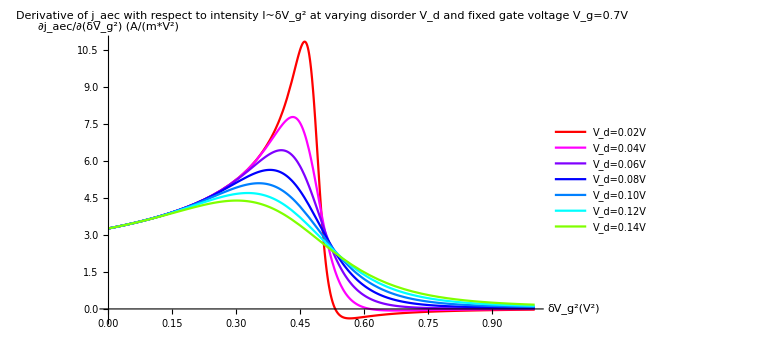

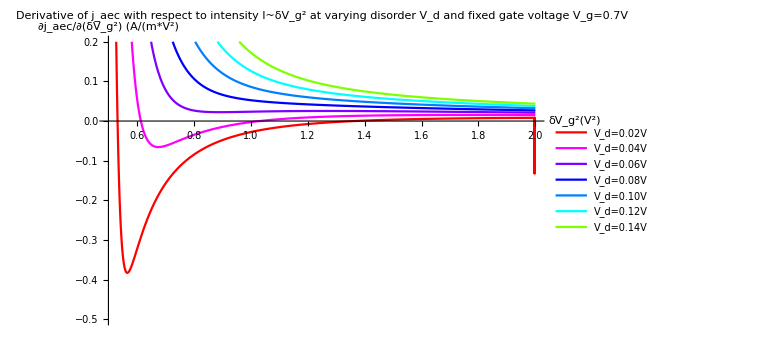

```mathematica
(*Plot[{F[0.1,δ^(1/2),Vd]/((G[0.1,δ^(1/2),Vd])^2),F[0.3,δ^(1/2),Vd]/((G[0.3,δ^(1/2),Vd])^2),F[0.5,δ^(1/2),Vd]/((G[0.5,δ^(1/2),Vd])^2),F[0.7,δ^(1/2),Vd]/((G[0.7,δ^(1/2),Vd])^2),F[0.9,δ^(1/2),Vd]/((G[0.9,δ^(1/2),Vd])^2),F[1.1,δ^(1/2),Vd]/((G[1.1,δ^(1/2),Vd])^2)},{δ,0,1},PlotLegends->{"V_g=0.1V","V_g=0.3V","V_g=0.5V","V_g=0.7V","V_g=0.9V","V_g=1.1V"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1]}]
Plot[{F[0.1,δ^(1/2),Vd]/(G[0.1,δ^(1/2),Vd]),F[0.3,δ^(1/2),Vd]/(G[0.3,δ^(1/2),Vd]),F[0.5,δ^(1/2),Vd]/(G[0.5,δ^(1/2),Vd]),F[0.7,δ^(1/2),Vd]/(G[0.7,δ^(1/2),Vd]),F[0.9,δ^(1/2),Vd]/(G[0.9,δ^(1/2),Vd]),F[1.1,δ^(1/2),Vd]/(G[1.1,δ^(1/2),Vd])},{δ,0,1},PlotLegends->{"V_g=0.1V","V_g=0.3V","V_g=0.5V","V_g=0.7V","V_g=0.9V","V_g=1.1V"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1]}]
Plot[{L[0.1,δ^(1/2),Vd],L[0.3,δ^(1/2),Vd],L[0.5,δ^(1/2),Vd],L[0.7,δ^(1/2),Vd],L[0.9,δ^(1/2),Vd],L[1.1,δ^(1/2),Vd]},{δ,0,1},PlotLegends->{"V_g=0.1V","V_g=0.3V","V_g=0.5V","V_g=0.7V","V_g=0.9V","V_g=1.1V"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1]}]
Plot[{L[0.1,δ^(1/2),Vd]/(F[0.1,δ^(1/2),Vd]/((G[0.1,δ^(1/2),Vd])^2)),L[0.3,δ^(1/2),Vd]/(F[0.3,δ^(1/2),Vd]/((G[0.3,δ^(1/2),Vd])^2)),L[0.5,δ^(1/2),Vd]/(F[0.5,δ^(1/2),Vd]/((G[0.5,δ^(1/2),Vd])^2)),L[0.7,δ^(1/2),Vd]/(F[0.7,δ^(1/2),Vd]/((G[0.7,δ^(1/2),Vd])^2)),L[0.9,δ^(1/2),Vd]/(F[0.9,δ^(1/2),Vd]/((G[0.9,δ^(1/2),Vd])^2)),L[1.1,δ^(1/2),Vd]/(F[1.1,δ^(1/2),Vd]/((G[1.1,δ^(1/2),Vd])^2))},{δ,0,1},PlotLegends->{"V_g=0.1V","V_g=0.3V","V_g=0.5V","V_g=0.7V","V_g=0.9V","V_g=1.1V"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1]}]
Plot[{L[0.1,δ^(1/2),Vd]/(F[0.1,δ^(1/2),Vd]/(G[0.1,δ^(1/2),Vd])),L[0.3,δ^(1/2),Vd]/(F[0.3,δ^(1/2),Vd]/(G[0.3,δ^(1/2),Vd])),L[0.5,δ^(1/2),Vd]/(F[0.5,δ^(1/2),Vd]/(G[0.5,δ^(1/2),Vd])),L[0.7,δ^(1/2),Vd]/(F[0.7,δ^(1/2),Vd]/(G[0.7,δ^(1/2),Vd])),L[0.9,δ^(1/2),Vd]/(F[0.9,δ^(1/2),Vd]/(G[0.9,δ^(1/2),Vd])),L[1.1,δ^(1/2),Vd]/(F[1.1,δ^(1/2),Vd]/(G[1.1,δ^(1/2),Vd]))},{δ,0,1},PlotLegends->{"V_g=0.1V","V_g=0.3V","V_g=0.5V","V_g=0.7V","V_g=0.9V","V_g=1.1V"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1]}]*)
Plot[{L[0.7,δ^(1/2),0.02],L[0.7,δ^(1/2),0.04],L[0.7,δ^(1/2),0.06],L[0.7,δ^(1/2),0.08],L[0.7,δ^(1/2),0.1],L[0.7,δ^(1/2),0.12],L[0.7,δ^(1/2),0.14]},{δ,0,1},PlotLegends->{"V_d=0.02V","V_d=0.04V","V_d=0.06V","V_d=0.08V","V_d=0.10V","V_d=0.12V","V_d=0.14V"},PlotLabel->"Derivative of j_aec with respect to intensity I~δV_g^2 at varying disorder V_d and fixed gate voltage V_g=0.7V",AxesLabel->{"δV_g^2(V^2)","∂j_aec/∂(δV_g^2) (A/(m*V^2)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
Plot[{L[0.7,δ^(1/2),0.02],L[0.7,δ^(1/2),0.04],L[0.7,δ^(1/2),0.06],L[0.7,δ^(1/2),0.08],L[0.7,δ^(1/2),0.1],L[0.7,δ^(1/2),0.12],L[0.7,δ^(1/2),0.14]},{δ,0.5,2},PlotRange->{-0.5,0.2},PlotLegends->{"V_d=0.02V","V_d=0.04V","V_d=0.06V","V_d=0.08V","V_d=0.10V","V_d=0.12V","V_d=0.14V"},PlotLabel->"Derivative of j_aec with respect to intensity I~δV_g^2 at varying disorder V_d and fixed gate voltage V_g=0.7V",AxesLabel->{"δV_g^2(V^2)","∂j_aec/∂(δV_g^2) (A/(m*V^2)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
```

-Graphics-

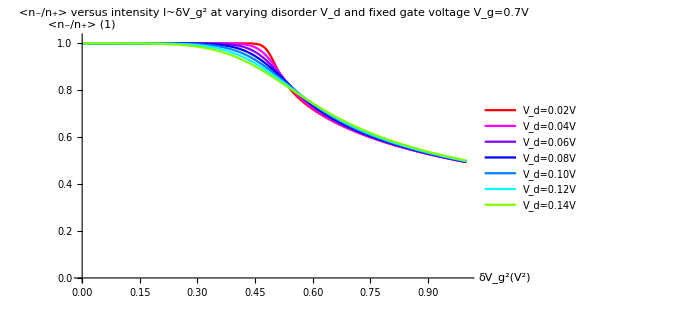

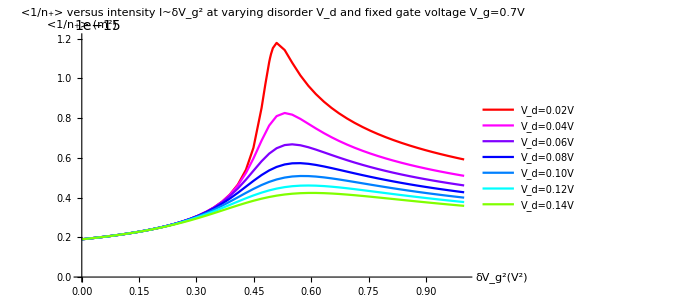

-Graphics-

```mathematica
Plot[{A[0.7,δ^(1/2),0.02]/B[0.7,δ^(1/2),0.02],A[0.7,δ^(1/2),0.04]/B[0.7,δ^(1/2),0.04],A[0.7,δ^(1/2),0.06]/B[0.7,δ^(1/2),0.06],A[0.7,δ^(1/2),0.08]/B[0.7,δ^(1/2),0.08],A[0.7,δ^(1/2),0.1]/B[0.7,δ^(1/2),0.1],A[0.7,δ^(1/2),0.12]/B[0.7,δ^(1/2),0.12],A[0.7,δ^(1/2),0.14]/B[0.7,δ^(1/2),0.14]},{δ,0,1},PlotRange->{0,5.4(10^15)},PlotLegends->{"V_d=0.02V","V_d=0.04V","V_d=0.06V","V_d=0.08V","V_d=0.10V","V_d=0.12V","V_d=0.14V"},PlotLabel->"<n_-/n_+>/<1/n_+> versus intensity I~δV_g^2 at varying disorder V_d and fixed gate voltage V_g=0.7V",AxesLabel->{"δV_g^2(V^2)","<n_-/n_+>/<1/n_+> (m^-2)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
Plot[{A[0.7,δ^(1/2),0.02],A[0.7,δ^(1/2),0.04],A[0.7,δ^(1/2),0.06],A[0.7,δ^(1/2),0.08],A[0.7,δ^(1/2),0.1],A[0.7,δ^(1/2),0.12],A[0.7,δ^(1/2),0.14]},{δ,0,1},PlotRange->{0,1.02},PlotLegends->{"V_d=0.02V","V_d=0.04V","V_d=0.06V","V_d=0.08V","V_d=0.10V","V_d=0.12V","V_d=0.14V"},PlotLabel->"<n_-/n_+> versus intensity I~δV_g^2 at varying disorder V_d and fixed gate voltage V_g=0.7V",AxesLabel->{"δV_g^2(V^2)","<n_-/n_+> (1)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
Plot[{B[0.7,δ^(1/2),0.02],B[0.7,δ^(1/2),0.04],B[0.7,δ^(1/2),0.06],B[0.7,δ^(1/2),0.08],B[0.7,δ^(1/2),0.1],B[0.7,δ^(1/2),0.12],B[0.7,δ^(1/2),0.14]},{δ,0,1},PlotRange->{0,1.2(10^-15)},PlotLegends->{"V_d=0.02V","V_d=0.04V","V_d=0.06V","V_d=0.08V","V_d=0.10V","V_d=0.12V","V_d=0.14V"},PlotLabel->"<1/n_+> versus intensity I~δV_g^2 at varying disorder V_d and fixed gate voltage V_g=0.7V",AxesLabel->{"δV_g^2(V^2)","<1/n_+> (m^2)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
Plot[{(B[0.7,δ^(1/2),0.02])^-1,(B[0.7,δ^(1/2),0.04])^-1,(B[0.7,δ^(1/2),0.06])^-1,(B[0.7,δ^(1/2),0.08])^-1,(B[0.7,δ^(1/2),0.1])^-1,(B[0.7,δ^(1/2),0.12])^-1,(B[0.7,δ^(1/2),0.14])^-1},{δ,0,1},PlotRange->{0,5.4(10^15)},PlotLegends->{"V_d=0.02V","V_d=0.04V","V_d=0.06V","V_d=0.08V","V_d=0.10V","V_d=0.12V","V_d=0.14V"},PlotLabel->"1/<1/n_+> versus intensity I~δV_g^2 at varying disorder V_d and fixed gate voltage V_g=0.7V",AxesLabel->{"δV_g^2(V^2)","1/<1/n_+> (m^-2)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
```

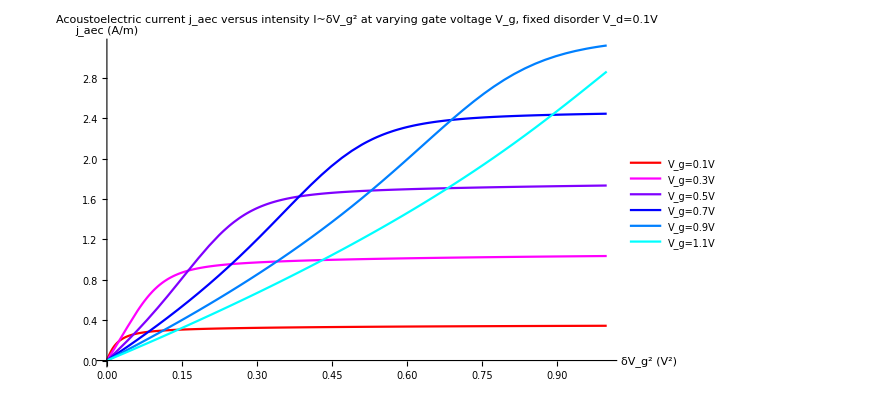

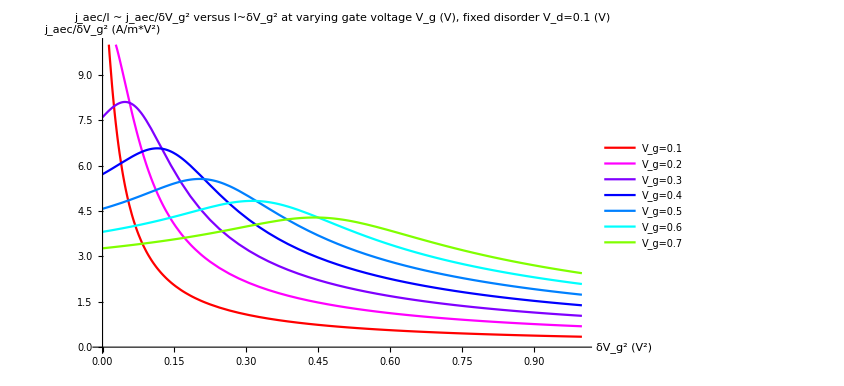

```mathematica
Plot[{Subscript[j, aec][0.1,δ^(1/2),Vd],Subscript[j, aec][0.3,δ^(1/2),Vd],Subscript[j, aec][0.5,δ^(1/2),Vd],Subscript[j, aec][0.7,δ^(1/2),Vd],Subscript[j, aec][0.9,δ^(1/2),Vd],Subscript[j, aec][1.1,δ^(1/2),Vd]},{δ,0,1},PlotLegends->{"V_g=0.1V","V_g=0.3V","V_g=0.5V","V_g=0.7V","V_g=0.9V","V_g=1.1V"},PlotLabel->"Acoustoelectric current j_aec versus intensity I~δV_g^2 at varying gate voltage V_g, fixed disorder V_d=0.1V",AxesLabel->{"δV_g^2 (V^2)","j_aec (A/m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1]}]
Plot[{1/δ Subscript[j, aec][0.1,δ^(1/2),Vd],1/δ Subscript[j, aec][0.2,δ^(1/2),Vd],1/δ Subscript[j, aec][0.3,δ^(1/2),Vd],1/δ Subscript[j, aec][0.4,δ^(1/2),Vd],1/δ Subscript[j, aec][0.5,δ^(1/2),Vd],1/δ Subscript[j, aec][0.6,δ^(1/2),Vd],1/δ Subscript[j, aec][0.7,δ^(1/2),Vd]},{δ,0,1},PlotRange->{0,10},PlotLegends->{"V_g=0.1","V_g=0.2","V_g=0.3","V_g=0.4","V_g=0.5","V_g=0.6","V_g=0.7"},PlotLabel->"j_aec/I ~ j_aec/δV_g^2 versus I~δV_g^2 at varying gate voltage V_g (V), fixed disorder V_d=0.1 (V)",AxesLabel->{"δV_g^2 (V^2)","j_aec/δV_g^2 (A/m*V^2)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
```

```mathematica
datSlide6a=Transpose[Prepend[Table[{δ,Subscript[j, aec][0.1,δ^(1/2),Vd],Subscript[j, aec][0.3,δ^(1/2),Vd],Subscript[j, aec][0.5,δ^(1/2),Vd],Subscript[j, aec][0.7,δ^(1/2),Vd],Subscript[j, aec][0.9,δ^(1/2),Vd],Subscript[j, aec][1.1,δ^(1/2),Vd]},{δ,0,1,dN[0,1,500]}]//N,{"δVg^2","Vg=0.1","Vg=0.3","Vg=0.5","Vg=0.7","V=0.9","V=1.1"}]];
datSlide6b=Transpose[Prepend[Table[{δ,1/δ Subscript[j, aec][0.1,δ^(1/2),Vd],1/δ Subscript[j, aec][0.2,δ^(1/2),Vd],1/δ Subscript[j, aec][0.3,δ^(1/2),Vd],1/δ Subscript[j, aec][0.4,δ^(1/2),Vd],1/δ Subscript[j, aec][0.5,δ^(1/2),Vd],1/δ Subscript[j, aec][0.6,δ^(1/2),Vd],1/δ Subscript[j, aec][0.7,δ^(1/2),Vd]},{δ,0.0001,1,dN[0.0001,1,500]}]//N,{"δVg^2","Vg=0.1","Vg=0.2","Vg=0.3","Vg=0.4","Vg=0.5","Vg=0.6","Vg=0.7"}]];
Export["Desktop/Mathematica/Graphene Integrals/(Slide 6a) Acoustoelectric current j_aec (A m^-1) versus intensity I~δVg^2 (V^2) at varying gate voltage Vg (V), fixed disorder Vd=0.1V.txt",datSlide6a]
Export["Desktop/Mathematica/Graphene Integrals/(Slide 6b) j_aec I^-1 ~ j_aec δVg^-2 (A m^-1 V^-2) versus intensity I~δVg^2 (V^2) at varying gate voltage Vg (V), fixed disorder Vd=0.1V.txt",datSlide6b]
```

Desktop/Mathematica/Graphene Integrals/(Slide 6a) Acoustoelectric current j_aec (A m^-1) versus intensity I~δVg^2 (V^2) at varying gate voltage Vg (V), fixed disorder Vd=0.1V.txt

Desktop/Mathematica/Graphene Integrals/(Slide 6b) j_aec I^-1 ~ j_aec δVg^-2 (A m^-1 V^-2) versus intensity I~δVg^2 (V^2) at varying gate voltage Vg (V), fixed disorder Vd=0.1V.txt

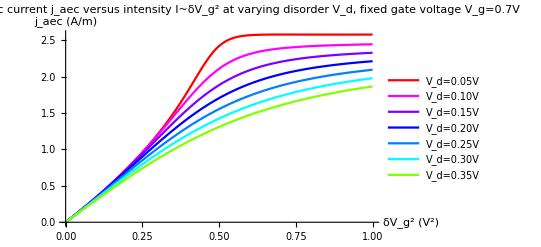

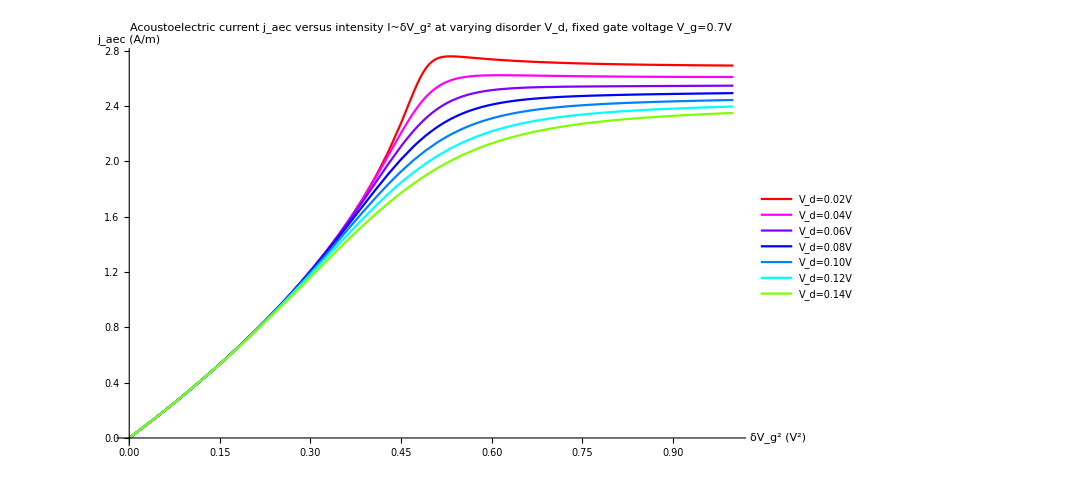

```mathematica
Plot[{Subscript[j, aec][vg2,δ^(1/2),0.05],Subscript[j, aec][vg2,δ^(1/2),0.10],Subscript[j, aec][vg2,δ^(1/2),0.15],Subscript[j, aec][vg2,δ^(1/2),0.20],Subscript[j, aec][vg2,δ^(1/2),0.25],Subscript[j, aec][vg2,δ^(1/2),0.30],Subscript[j, aec][vg2,δ^(1/2),0.35]},{δ,0,1},PlotLegends->{"V_d=0.05V","V_d=0.10V","V_d=0.15V","V_d=0.20V","V_d=0.25V","V_d=0.30V","V_d=0.35V"},PlotLabel->"Acoustoelectric current j_aec versus intensity I~δV_g^2 at varying disorder V_d, fixed gate voltage V_g=0.7V",AxesLabel->{"δV_g^2 (V^2)","j_aec (A/m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}] 
Plot[{Subscript[j, aec][vg2,δ^(1/2),0.02],Subscript[j, aec][vg2,δ^(1/2),0.04],Subscript[j, aec][vg2,δ^(1/2),0.06],Subscript[j, aec][vg2,δ^(1/2),0.08],Subscript[j, aec][vg2,δ^(1/2),0.10],Subscript[j, aec][vg2,δ^(1/2),0.12],Subscript[j, aec][vg2,δ^(1/2),0.14]},{δ,0,1},PlotLegends->{"V_d=0.02V","V_d=0.04V","V_d=0.06V","V_d=0.08V","V_d=0.10V","V_d=0.12V","V_d=0.14V"},PlotLabel->"Acoustoelectric current j_aec versus intensity I~δV_g^2 at varying disorder V_d, fixed gate voltage V_g=0.7V",AxesLabel->{"δV_g^2 (V^2)","j_aec (A/m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
```

```mathematica
datSlide14=Transpose[Prepend[Table[{δ,Subscript[j, aec][vg2,δ^(1/2),0.02],Subscript[j, aec][vg2,δ^(1/2),0.04],Subscript[j, aec][vg2,δ^(1/2),0.06],Subscript[j, aec][vg2,δ^(1/2),0.08],Subscript[j, aec][vg2,δ^(1/2),0.10],Subscript[j, aec][vg2,δ^(1/2),0.12],Subscript[j, aec][vg2,δ^(1/2),0.14]},{δ,0,1,dN[0,1,500]}]//N,{"δVg^2","Vd=0.02","Vd=0.04","Vd=0.06","Vd=0.08","Vd=0.10","Vd=0.12","Vd=0.12"}]];
Export["Desktop/Mathematica/Graphene Integrals/(Slide 14) Acoustoelectric current j_aec (A m^-1) versus intensity I~δVg^2 (V^2) at varying disorder Vd (V), fixed gate voltage Vg=0.7V.txt",datSlide14]
```

Desktop/Mathematica/Graphene Integrals/(Slide 14) Acoustoelectric current j_aec (A m^-1) versus intensity I~δVg^2 (V^2) at varying disorder Vd (V), fixed gate voltage Vg=0.7V.txt

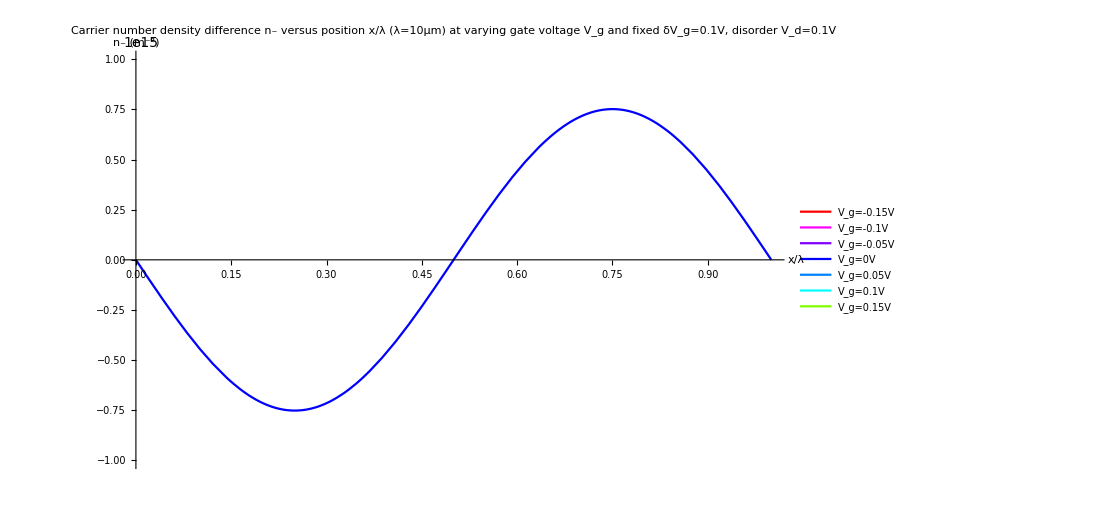

```mathematica
Plot[{nm[Vg[-0.15,δVg,λ x],Vd],nm[Vg[-0.1,δVg,λ x],Vd],nm[Vg[-0.05,δVg,λ x],Vd],nm[Vg[0,δVg,λ x],Vd],nm[Vg[0.05,δVg,λ x],Vd],nm[Vg[0.1,δVg,λ x],Vd],nm[Vg[0.15,δVg,λ x],Vd]},{x,0,1},PlotLegends->{"V_g=-0.15V","V_g=-0.1V","V_g=-0.05V","V_g=0V","V_g=0.05V","V_g=0.1V","V_g=0.15V"},PlotLabel->"Carrier number density difference n_- versus position x/λ (λ=10μm) at varying gate voltage V_g and fixed δV_g=0.1V, disorder V_d=0.1V",AxesLabel->{"x/λ","n_- (m^-2)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
```

```mathematica
datSlide8=Transpose[Prepend[Table[{x,nm[Vg[-0.15,δVg,λ x],Vd],nm[Vg[-0.1,δVg,λ x],Vd],nm[Vg[-0.05,δVg,λ x],Vd],nm[Vg[0,δVg,λ x],Vd],nm[Vg[0.05,δVg,λ x],Vd],nm[Vg[0.1,δVg,λ x],Vd],nm[Vg[0.15,δVg,λ x],Vd]},{x,0,1,dN[0,1,500]}]//N,{"x/λ","Vg=-0.15","Vg=-0.1","Vg=-0.05","Vg=0","Vg=0.05","Vg=0.1","Vg=0.15"}]];
Export["Desktop/Mathematica/Graphene Integrals/(Slide 8) Carrier number density difference n- (m^-2) versus position x λ^-1 (λ=10μm) at varying gate voltage Vg (V) and fixed δVg=0.1V, disorder Vd=0.1V.txt",datSlide8]
```

Desktop/Mathematica/Graphene Integrals/(Slide 8) Carrier number density difference n- (m^-2) versus position x λ^-1 (λ=10μm) at varying gate voltage Vg (V) and fixed δVg=0.1V, disorder Vd=0.1V.txt

General::munfl: Exp[-1249.36] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

General::munfl: Exp[-1249.36] is too small to represent as a normalized machine number; precision may be lost.

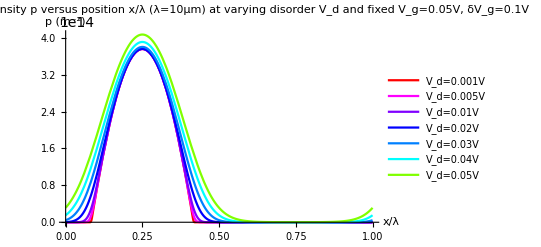

```mathematica
Plot[{n[Vg[0.05,δVg,λ x],0.001],n[Vg[0.05,δVg,λ x],0.005],n[Vg[0.05,δVg,λ x],0.01],n[Vg[0.05,δVg,λ x],0.02],n[Vg[0.05,δVg,λ x],0.03],n[Vg[0.05,δVg,λ x],0.04],n[Vg[0.05,δVg,λ x],0.05]},{x,0,1},PlotLegends->{"V_d=0.001V","V_d=0.005V","V_d=0.01V","V_d=0.02V","V_d=0.03V","V_d=0.04V","V_d=0.05V"},PlotLabel->"Electron number density n versus position x/λ (λ=10μm) at varying disorder V_d and fixed V_g=0.05V, δV_g=0.1V",AxesLabel->{"x/λ","n (m^-2)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
Plot[{p[Vg[0.05,δVg,λ x],0.001],p[Vg[0.05,δVg,λ x],0.005],p[Vg[0.05,δVg,λ x],0.01],p[Vg[0.05,δVg,λ x],0.02],p[Vg[0.05,δVg,λ x],0.03],p[Vg[0.05,δVg,λ x],0.04],p[Vg[0.05,δVg,λ x],0.05]},{x,0,1},PlotLegends->{"V_d=0.001V","V_d=0.005V","V_d=0.01V","V_d=0.02V","V_d=0.03V","V_d=0.04V","V_d=0.05V"},PlotLabel->"Hole number density p versus position x/λ (λ=10μm) at varying disorder V_d and fixed V_g=0.05V, δV_g=0.1V",AxesLabel->{"x/λ","p (m^-2)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
```

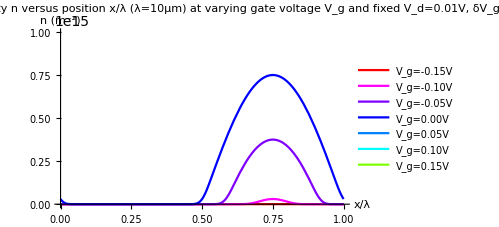

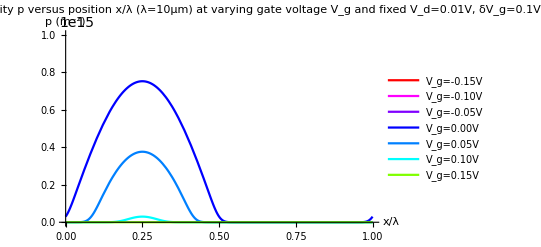

```mathematica
vd2=0.01;
Plot[{n[Vg[-0.15,δVg,λ x],vd2],n[Vg[-0.1,δVg,λ x],vd2],n[Vg[-0.05,δVg,λ x],vd2],n[Vg[0,δVg,λ x],vd2],n[Vg[0.05,δVg,λ x],vd2],n[Vg[0.10,δVg,λ x],vd2],n[Vg[0.15,δVg,λ x],vd2]},{x,0,1},PlotLegends->{"V_g=-0.15V","V_g=-0.10V","V_g=-0.05V","V_g=0.00V","V_g=0.05V","V_g=0.10V","V_g=0.15V"},PlotLabel->"Electron number density n versus position x/λ (λ=10μm) at varying gate voltage V_g and fixed V_d=0.01V, δV_g=0.1V",AxesLabel->{"x/λ","n (m^-2)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
Plot[{p[Vg[-0.15,δVg,λ x],vd2],p[Vg[-0.1,δVg,λ x],vd2],p[Vg[-0.05,δVg,λ x],vd2],p[Vg[0,δVg,λ x],vd2],p[Vg[0.05,δVg,λ x],vd2],p[Vg[0.10,δVg,λ x],vd2],p[Vg[0.15,δVg,λ x],vd2]},{x,0,1},PlotLegends->{"V_g=-0.15V","V_g=-0.10V","V_g=-0.05V","V_g=0.00V","V_g=0.05V","V_g=0.10V","V_g=0.15V"},PlotLabel->"Hole number density p versus position x/λ (λ=10μm) at varying gate voltage V_g and fixed V_d=0.01V, δV_g=0.1V",AxesLabel->{"x/λ","p (m^-2)"},PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
```

```mathematica
datSlide19a=Transpose[Prepend[Table[{x,n[Vg[-0.15,δVg,λ x],vd2],n[Vg[-0.1,δVg,λ x],vd2],n[Vg[-0.05,δVg,λ x],vd2],n[Vg[0,δVg,λ x],vd2],n[Vg[0.05,δVg,λ x],vd2],n[Vg[0.10,δVg,λ x],vd2],n[Vg[0.15,δVg,λ x],vd2]},{x,0,1,dN[0,1,500]}]//N,{"x/λ","Vg=-0.15","Vg=-0.10","Vg=-0.05","Vg=0.00","Vg=0.05","Vg=0.10","Vg=0.15"}]];
datSlide19b=Transpose[Prepend[Table[{x,p[Vg[-0.15,δVg,λ x],vd2],p[Vg[-0.1,δVg,λ x],vd2],p[Vg[-0.05,δVg,λ x],vd2],p[Vg[0,δVg,λ x],vd2],p[Vg[0.05,δVg,λ x],vd2],p[Vg[0.10,δVg,λ x],vd2],p[Vg[0.15,δVg,λ x],vd2]},{x,0,1,dN[0,1,500]}]//N,{"x/λ","Vg=-0.15","Vg=-0.10","Vg=-0.05","Vg=0.00","Vg=0.05","Vg=0.10","Vg=0.15"}]];
Export["Desktop/Mathematica/Graphene Integrals/(Slide 19a) Electron number density n (m^-2) versus position x λ^-1 (λ=10μm) at varying gate voltage Vg (V) and fixed Vd=0.01V, δVg=0.1V.txt",datSlide19a]
Export["Desktop/Mathematica/Graphene Integrals/(Slide 19b) Hole number density p (m^-2) versus position x λ^-1 (λ=10μm) at varying gate voltage Vg (V) and fixed Vd=0.01V, δVg=0.1V.txt",datSlide19b]
```

Desktop/Mathematica/Graphene Integrals/(Slide 19a) Electron number density n (m^-2) versus position x λ^-1 (λ=10μm) at varying gate voltage Vg (V) and fixed Vd=0.01V, δVg=0.1V.txt

Desktop/Mathematica/Graphene Integrals/(Slide 19b) Hole number density p (m^-2) versus position x λ^-1 (λ=10μm) at varying gate voltage Vg (V) and fixed Vd=0.01V, δVg=0.1V.txt

```mathematica
Plot[{nm[Vg[0.05,δVg,λ x],Vd],np[Vg[0.05,δVg,λ x],0.001],np[Vg[0.05,δVg,λ x],0.005],np[Vg[0.05,δVg,λ x],0.01],np[Vg[0.05,δVg,λ x],0.02],np[Vg[0.05,δVg,λ x],0.03],np[Vg[0.05,δVg,λ x],0.04],np[Vg[0.05,δVg,λ x],0.05]},{x,0,1},PlotLegends->{"n_-","V_d=0.001V","V_d=0.005V","V_d=0.01V","V_d=0.02V","V_d=0.03V","V_d=0.04V","V_d=0.05V"},PlotLabel->"Carrier number density difference n_- and total n_+ versus position x/λ (λ=10μm) at varying disorder V_d and fixed V_g=0.05V, δV_g=0.1V",AxesLabel->{"x/λ","n_± (m^-2)"},PlotStyle->{Black,RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
Plot[{nm[Vg[0.05,δVg,λ x],Vd]},{x,0,1},PlotLegends->{"n_-"},PlotLabel->"Carrier number density difference n_- versus position x/λ (λ=10μm) at fixed V_g=0.05V, δV_g=0.1V, and disorder V_d=0.1V",AxesLabel->{"x/λ","n_- (m^-2)"}]
```

General::munfl: Exp[-1249.36] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

-Graphics-

General::munfl: Exp[-1249.36] is too small to represent as a normalized machine number; precision may be lost.

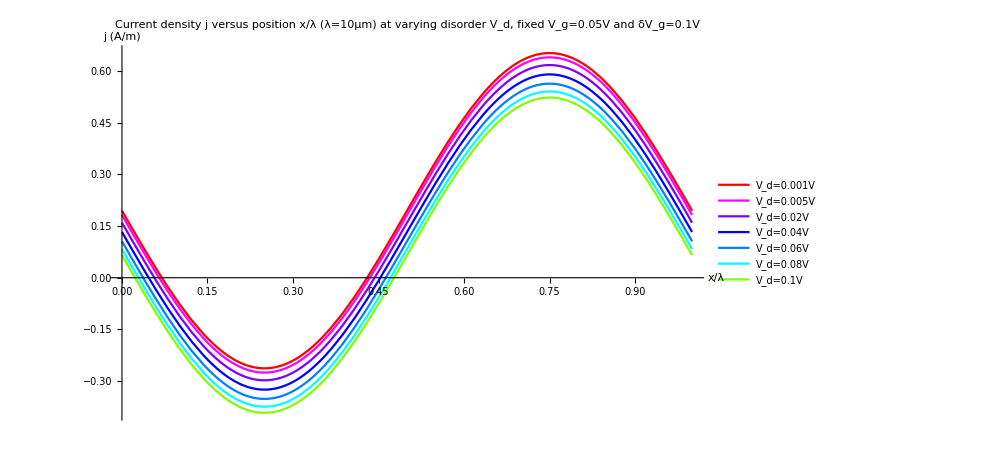

```mathematica
Plot[{j[0.05,δVg,0.001,λ x],j[0.05,δVg,0.005,λ x],j[0.05,δVg,0.02,λ x],j[0.05,δVg,0.04,λ x],j[0.05,δVg,0.06,λ x],j[0.05,δVg,0.08,λ x],j[0.05,δVg,0.1,λ x]},{x,0,1},PlotLegends->{"V_d=0.001V","V_d=0.005V","V_d=0.02V","V_d=0.04V","V_d=0.06V","V_d=0.08V","V_d=0.1V"},AxesLabel->{"x/λ","j (A/m)"},PlotLabel->"Current density j versus position x/λ (λ=10μm) at varying disorder V_d, fixed V_g=0.05V and δV_g=0.1V",PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,1],RGBColor[0.5,0,1],RGBColor[0,0,1],RGBColor[0,0.5,1],RGBColor[0,1,1],RGBColor[0.5,1,0]}]
```